Number of N-ary Algebras: number of n-ary functions from some set to that set, functions with n arguments

1 arg:
http://oeis.org/A001372 - Number of mappings (or mapping patterns) from n points to themselves; number of endofunctions.
http://oeis.org/A000312 - a(n) = n^n; number of labeled mappings from n points to themselves (endofunctions). 
2 args:
http://oeis.org/A001329 - Number of nonisomorphic groupoids with n elements. 
https://oeis.org/A002489 - a(n) = n^(n^2), or (n^n)^n. -- labeled groupoids
3 args:
http://oeis.org/A091510 - Number of nonisomorphic algebras with a ternary operation (3-d groupoids) with n elements. 

The formula for the number of nonisomorphic algebras is a general one, and it works for one argument.

For more than one arg, the asymptotic number of algebras for number of args m and domain size n is (labeled number) / n! where (labeled number) is n^(n^m). It does not work for only one arg, underestimating by an amount that is roughly 1.11047 * 1.08736^n.

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"Partition Transform.nb"];
```

## Data

```mathematica
(* Zero-based: *)
```

```mathematica
numdata["nary",1] = {1,1,3,7,19,47,130,343,951,2615,7318,20491,57903,163898,466199,1328993,3799624,10884049,31241170,89814958,258604642,745568756,2152118306,6218869389,17988233052,52078309200,150899223268,437571896993,1269755237948,3687025544605,10712682919341,31143566495273,90587953109272,263627037547365};
```

```mathematica
numdata["nary lbl",1] = {1,1,4,27,256,3125,46656,823543,16777216,387420489,10000000000,285311670611,8916100448256,302875106592253,11112006825558016,437893890380859375,18446744073709551616,827240261886336764177,39346408075296537575424,1978419655660313589123979};
```

```mathematica
numdata["nary",2] = {1,1,10,3330,178981952,2483527537094825,14325590003318891522275680,50976900301814584087291487087214170039,155682086691137947272042502251643461917498835481022016};
```

```mathematica
numdata["nary lbl",2] = {1,1,16,19683,4294967296,298023223876953125,10314424798490535546171949056,256923577521058878088611477224235621321607,6277101735386680763835789423207666416102355444464034512896,196627050475552913618075908526912116283103450944214766927315415537966391196809};
```

```mathematica
numdata["nary",3] = {1,1,136,1270933717887,14178431955039102651224805804387336192,19591572513704791799478942287037427963655716808579364910828644498251439742675781250000};
```

## Formulas

```mathematica
SetAttributes[numval,Listable]
```

```mathematica
isposint[n_] := If[Head[n]===Integer,n>0,False]
```

```mathematica
ispzint[n_] := If[Head[n]===Integer,n≥0,False]
```

```mathematica
(* All labeled *)
```

```mathematica
numval["nary lbl",mpwr_?ispzint,n_?ispzint] := If[n>0,n^(n^mpwr),1]
```

```mathematica
(* One arg -- lists starting at zero index *)
```

```mathematica
numrootedtrees[nmax_?ispzint] := Module[{a},
a[n_]:=a[n]=If[n≤1,n,Sum[DivisorSum[j,#*a[#]&]*a[n-j],{j,1,n-1}]/(n-1)];
Array[a,nmax+1,0]
]
```

```mathematica
numlistval["nary",1,nmax_?ispzint] := Module[{nroot,afn,x,gen},
nroot = numrootedtrees[nmax];
afn[t_] := nroot.t^Range[0,nmax];
gen = 1/Product[1-afn[x^n],{n,nmax}];
CoefficientList[Series[gen,{x,0,nmax}],x]
]
```

```mathematica
NumPartitions[n_] := Module[{indpart,nlst},
nlst = Range[n];
indpart[p_] := (Last /@ Sort[Tally[Join[p,nlst]]])-1;
indpart /@ IntegerPartitions[n]
]
```

```mathematica
PartMult[p_] := Module[{l,n},
l = Length[p];
n = Sum[i*p[[i]],{i,l}];
n!/Product[p[[i]]!*i^p[[i]],{i,l}]
]
```

```mathematica
pwr[x_,n_] := If[n==0,1,x^n]
```

```mathematica
dpdlsum[p_,ilst_] := Module[{n,dvs,d},
n = Length[p];
dvs = Select[Divisors[LCM @@ ilst],#≤n&];
Sum[d*p[[d]],{d,dvs}]
]
```

```mathematica
numval["nary",mpwr_?ispzint,n_?ispzint] := Module[{ps,ngps,ilst,p},
ps = NumPartitions[n];
ngps[p_] := Product[
pwr[dpdlsum[p,ilst],(Product[p[[i]],{i,ilst}]*(Times  @@ ilst)/(LCM @@ ilst))],
{ilst,Tuples[Range[n],mpwr]}];
(1/n!)*Sum[PartMult[p]*ngps[p],{p,ps}]
]
```

## Tests

```mathematica
nvtest[lbl_,mpwr_] := (nd|-> nd - numval[lbl,mpwr,Range[Length[nd]]-1])[numdata[lbl,mpwr]]
```

```mathematica
nvtest[lbl_,mpwr_,clip_] := (nd|-> nd - numval[lbl,mpwr,Range[Length[nd]]-1])[Take[numdata[lbl,mpwr],clip]]
```

```mathematica
nvtest["nary lbl",1] // Tally
```

{{0,20}}

```mathematica
nvtest["nary lbl",2] // Tally
```

{{0,10}}

```mathematica
nvtest["nary",1,15] // Tally
```

{{0,15}}

```mathematica
nvtest["nary",2] // Tally
```

{{0,9}}

```mathematica
nvtest["nary",3] // Tally
```

{{0,6}}

```mathematica
(* with the specific formula in OEIS *)
```

```mathematica
(nd|-> nd - numlistval["nary",1,Length[nd]-1])[numdata["nary",1]] // Tally
```

{{0,34}}

## Asymptotic behavior

```mathematica
SetAttributes[numasymp,Listable]
```

```mathematica
numasymp["nary",mpwr_,n_] := n^(n^mpwr)/n!
```

```mathematica
numasymptest["nary",mpwr_] := (nd |-> nd/numasymp["nary",mpwr,N[Range[Length[nd]]]])[Rest[numdata["nary",mpwr]]]
```

```mathematica
numasymptest["nary",2]
```

{1.,1.25,1.01509,1.00014,1.,1.,1.,1.}

```mathematica
numasymptest["nary",3]
```

{1.,1.0625,1.,1.,1.}

```mathematica
numasymptest["nary",1]
```

{1.,1.5,1.55556,1.78125,1.8048,2.00617,2.09913,2.2855,2.44936,2.65556,2.86681,3.11074,3.36969,3.65752,3.96875,4.30964,4.6798,5.0835,5.52236,6.00013,6.51968,7.0849,7.69956,8.36805,9.09499,9.88551,10.7451,11.6798,12.6962,13.8013,15.003,16.3096,17.7303}

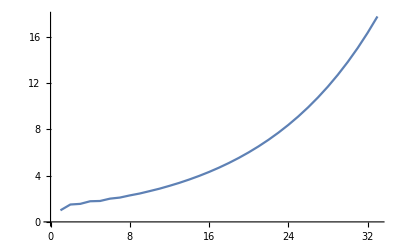

```mathematica
ListPlot[%,Joined->True]
```

```mathematica
asympdscr[nmax_] := Rest[numlistval["nary",1,nmax]]/numasymp["nary",1,N[Range[nmax]]]
```

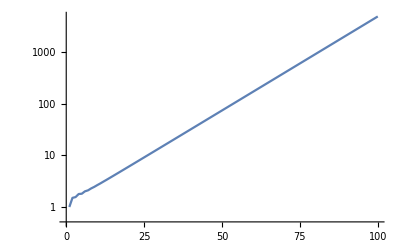

```mathematica
ListLogPlot[asympdscr[100],Joined->True]
```

```mathematica
SetAttributes[fixfunc,Listable]
```

```mathematica
asympdscrfix[nmax_] := Rest[numlistval["nary",1,nmax]]/numasymp["nary",1,N[Range[nmax]]]
```

```mathematica
fixfunc[n_] := 0.083756*n+0.10478 + 0.183898/n+1.05886/n^2
```

```mathematica
Log[asympdscrfix[100]] - fixfunc[Range[100]]
```

{-1.43129,-0.223491,-0.0931657,0.0253581,-0.0122442,0.0288504,0.00256823,0.0122247,0.0037362,0.00533559,0.00163598,0.00232915,0.000802324,0.00088451,0.000364527,0.000347426,0.000142077,0.000128258,0.0000497003,0.0000399143,0.0000115315,7.10332×10^-6,-2.63261×10^-6,-3.58377×10^-6,-6.12584×10^-6,-5.53313×10^-6,-5.40977×10^-6,-4.24837×10^-6,-3.29809×10^-6,-2.07045×10^-6,-1.00392×10^-6,6.33027×10^-8,9.82947×10^-7,1.81265×10^-6,2.50752×10^-6,3.09337×10^-6,3.56178×10^-6,3.92852×10^-6,4.19763×10^-6,4.38112×10^-6,4.48668×10^-6,4.52426×10^-6,4.50196×10^-6,4.42817×10^-6,4.31024×10^-6,4.1552×10^-6,3.96934×10^-6,3.75848×10^-6,3.52784×10^-6,3.28215×10^-6,3.02569×10^-6,2.76227×10^-6,2.49532×10^-6,2.22791×10^-6,1.96277×10^-6,1.70231×10^-6,1.44869×10^-6,1.2038×10^-6,9.69321×10^-7,7.46718×10^-7,5.37276×10^-7,3.42116×10^-7,1.62208×10^-7,-1.61203×10^-9,-1.48628×10^-7,-2.78233×10^-7,-3.89918×10^-7,-4.8326×10^-7,-5.57914×10^-7,-6.13608×10^-7,-6.50128×10^-7,-6.67321×10^-7,-6.6508×10^-7,-6.43345×10^-7,-6.02095×10^-7,-5.41344×10^-7,-4.61138×10^-7,-3.61551×10^-7,-2.42679×10^-7,-1.04644×10^-7,5.24168×10^-8,2.28348×10^-7,4.2298×10^-7,6.3613×10^-7,8.67605×10^-7,1.1172×10^-6,1.38471×10^-6,1.66992×10^-6,1.97259×10^-6,2.29252×10^-6,2.62946×10^-6,2.98318×10^-6,3.35344×10^-6,3.74002×10^-6,4.14266×10^-6,4.56114×10^-6,4.99522×10^-6,5.44465×10^-6,5.90921×10^-6,6.38866×10^-6}